```mathematica
Quit[];
```

```mathematica
(*healthy state*)
Wss=0;
Wgs=1.12;
Wsg=19;
Wgg=6.6;
Wcs=2.42;
Wxg=15.1;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS= 6;(* tau_s = tau_g *);
```

```mathematica
(* Rescaled System's coefficients and function definition *)
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_]:={
-u[[1]]+f1[tu+ac*ud[[1]]+bc*ud[[2]]],
-u[[2]]+f2[tv+cc*ud[[1]]+dc*ud[[2]]]}
```

```mathematica
(*equilibrium point*)
eq={u,v}/.FindRoot[F[{u,v},{u,v}]=={0,0},{{u,0},{v,0}}]
```

{18.1475,53.693}

```mathematica
(*characteristic parameter values*)
alpha=ac*f1'[tu+ac*eq[[1]]+bc*eq[[2]]]+dc*f2'[tv+cc*eq[[1]]+dc*eq[[2]]]
beta=(ac*dc-bc*cc)*f1'[tu+ac*eq[[1]]+bc*eq[[2]]]*f2'[tv+cc*eq[[1]]+dc*eq[[2]]]
```

-3.06805

2.24878

```mathematica
(*Weak Gamma kernel - Laplace transform and related functions defined in paper*)
H[z_]:=1/(1+z);
Q[t_,z_]:=(z+t)/(t*H[z]);
al[t_,w_]:=2*Re[Q[t,I*w]];
be[t_,w_]:=Abs[Q[t,I*w]]^2;
Co[t_,w_]:=Re[H[I*w]];
rho[w_]:=1/Sqrt[1+w^2]; (*given explicitely for ease of computation*)
theta[w_]:=ArcTan[w]; (*given explicitely for ease of computation*)
```

```mathematica
(*No critical value of tau such that (alpha,beta) is exactly on the curve (gamma_tau)*)
NSolve[beta==(1-alpha/2)^2+(tau+1/tau)*(1-alpha/2)+1&&tau>0,tau,Reals]
```

{}

```mathematica
Tau=0.61942;
(*stability region for Strong Gamma kernel, together with point of coordinates (alpha, beta) - uses range accoring to bifurcation values, so that domains can be compared - using inequalities in Example 2.2*)
pw[t_]:=
Show[RegionPlot[x-1<y<(1-x/2)^2+(t+1/t)*(1-x/2)+1&&x<2,{x,-10,2},{y,-12,20},PlotPoints->100],
Plot[x-1,{x,-10,2},PlotStyle->Red],
Graphics[{Red,PointSize[0.04],Point[{alpha,beta}]}],
LabelStyle->Directive[Bold,Black, FontSize->20],ImageSize->{Automatic,300},
Epilog->Inset[Framed[Style[Row[{"W. Gamma, τ=",t}],Bold,19],Background->LightYellow,RoundingRadius->4],{-1,15}],
PlotRange->{{-4,2},{-5,17}}]
```

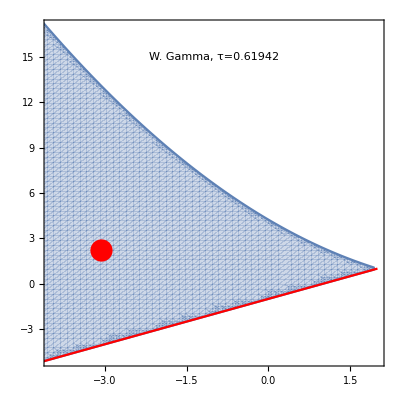

```mathematica
pw[Tau]
```

```mathematica
(*system with WEAK GAMMA kernel - using linear chain trick*)
sys[tau_]:={u'[t]==F[{u[t],v[t]},{ud1[t],vd1[t]}][[1]],
v'[t]==F[{u[t],v[t]},{ud1[t],vd1[t]}][[2]],
ud1'[t]==(u[t]-ud1[t])/tau,
vd1'[t]==(v[t]-vd1[t])/tau,
u[0]==0,
v[0]==0,
ud1[0]==0,
vd1[0]==0};
```

```mathematica
(*plot evolution of state variables*)
trans=0;Tmax=160/1.2;
p1[tau_]:=Plot[Evaluate[{u[(t+trans)/(tauS*10^(-3))],v[(t+trans)/(tauS*10^(-3))]} /. NDSolve[sys[tau],{u,v,ud1,vd1},{t,Tmax}]],{t,0,(Tmax-trans)*tauS*10^(-3)},PlotRange->All,Axes->False,Frame->True, PlotStyle->{{Thick,Red},{Thick,Blue}},FrameLabel->{None,"STN, GP vs. time (s)"},ImageSize->{Automatic,300},LabelStyle->Directive[Bold,Black, FontSize->20]]
```

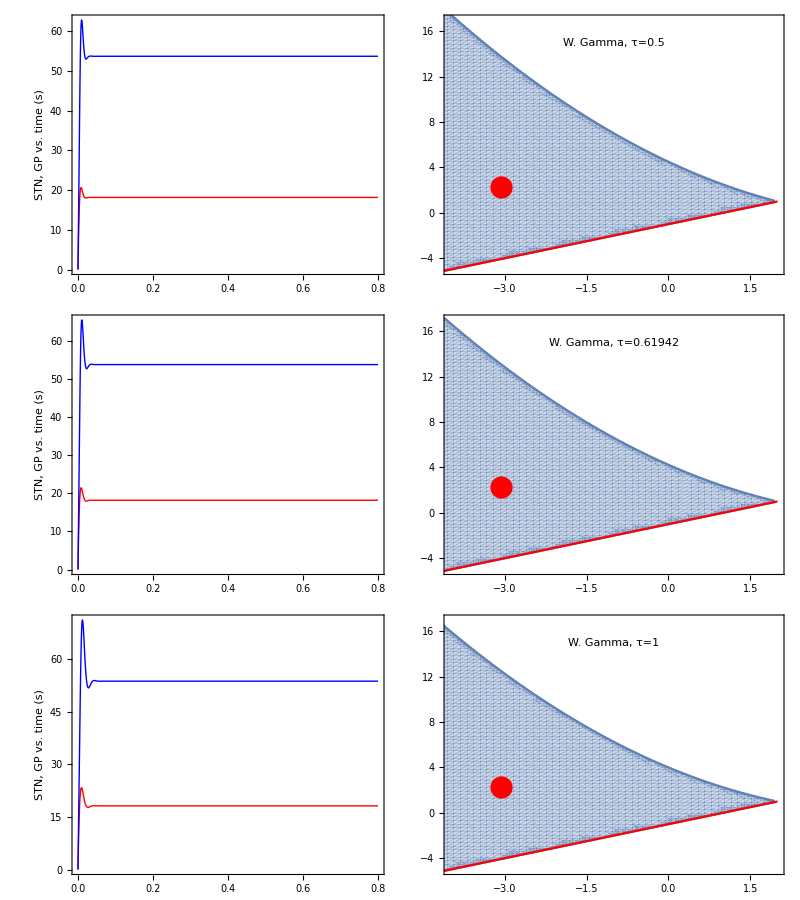

```mathematica
(*Graphics: evolution of state variables vs. stability domain*)
Grid[{{p1[0.5],pw[0.5]},{p1[Tau],pw[Tau]},{p1[1],pw[1]}}]
```